Based on: F0Cleaned.nb [Kerr Doran period -- Full]
We test whether Li2Rules we need actually hold over the range of R we are interested in

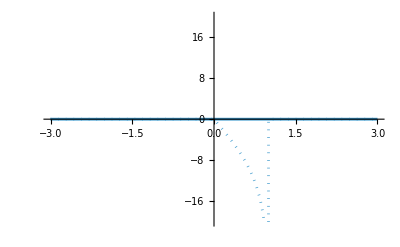

```mathematica
ReImPlot[Li2[(1+R)/(1-R)]-1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2)/.Li2Eval, {R, -3, 3},
PlotRange->{Automatic, {-20, 20}}
]
```

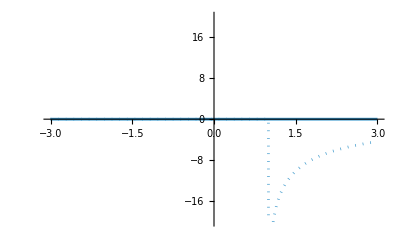

```mathematica
ReImPlot[Li2[(1+R)/(-1+R)]-1/6 (-π^2-6 Li2[(-1+R)/(1+R)]-3 Log[-(-1+R)/(1+R)]^2)/.Li2Eval, {R, -3, 3},
PlotRange->{Automatic, {-20, 20}}
]
```

```mathematica
D[PolyLog[2,z], z]
```

-Log[1-z]/z

```mathematica
Li2[(1+R)/(1-R)]-1/6 (-π^2-6 Li2[(1-R)/(1+R)]-3 Log[(-1+R)/(1+R)]^2)
FullSimplify[R D[%, R], R∈Complexes]/.{Li2'[z_]:>-Log[1-z]/z}//FullSimplify[#, R∈Complexes]&
FullSimplify[R D[%, R], R∈Complexes]
```

Li2[(1+R)/(1-R)]+1/6 (π^2+6 Li2[(1-R)/(1+R)]+3 Log[(-1+R)/(1+R)]^2)

(2 R (-Log[1-R]+Log[-1+R]+Log[-R]-Log[R]))/(-1+R^2)

(2 R (1+R^2) (Log[1-R]-Log[-1+R]-Log[-R]+Log[R]))/((-1+R^2)^2)

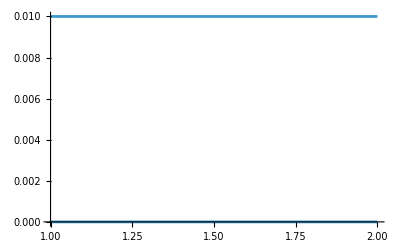

```mathematica
Plot[{Re[#], Im[#]+.01}&@((2 R (1+R^2) (Log[1-R]-Log[-1+R]-Log[-R]+Log[R]))/((-1+R^2)^2)), {R, 1, 2}]
```

```mathematica
Plot3D[Im[(2 R (1+R^2) (Log[1-R]-Log[-1+R]-Log[-R]+Log[R]))/((-1+R^2)^2)/.{R->R1+I R2}], {R1,-3, 3}, {R2,-3,3},
PlotRange->{Automatic, Automatic, {-4, 4}}
]
```

-Graphics3D-

```mathematica
Expand[Pi B1]
Map[Together, %/.{Li2->Subscript[Li, 2]}, Infinity]
```

Li2[(-1+R)/(1+R)]+Li2[(1+R)/(1-R)]-Li2[(1+R)/(-1+R)]-Li2[-1+2/(1+R)]+ⅈ π Log[-1+R]+2 ⅈ π Log[R]-2 Log[-1+R] Log[R]-ⅈ π Log[1+R]+2 Log[R] Log[1+R]

ⅈ π Log[-1+R]+2 ⅈ π Log[R]-2 Log[-1+R] Log[R]-ⅈ π Log[1+R]+2 Log[R] Log[1+R]+Li_2[(-1-R)/(-1+R)]-Li_2[(1-R)/(1+R)]+Li_2[(-1+R)/(1+R)]-Li_2[(1+R)/(-1+R)]

```mathematica
Expand[Pi B2]
Map[Together, %/.{Li2->Subscript[Li, 2]}, Infinity]
%/.{Log[(1-R)/(1+R)]->I Pi + Log[(R-1)/(1+R)]}//Expand//Simplify
%/.{Log[(-1+R)/(1+R)]->Log[R-1]-Log[R+1]}//Expand//Simplify
```

2 Li2[(-1+R)/(1+R)]-2 Li2[-1+2/(1+R)]+ⅈ π Log[-1+R]+2 ⅈ π Log[R]-2 Log[-1+R] Log[R]-1/2 Log[(-1+R)/(1+R)]^2-ⅈ π Log[1+R]+2 Log[R] Log[1+R]+1/2 Log[-1+2/(1+R)]^2

ⅈ π Log[-1+R]+2 ⅈ π Log[R]-2 Log[-1+R] Log[R]+1/2 Log[(1-R)/(1+R)]^2-1/2 Log[(-1+R)/(1+R)]^2-ⅈ π Log[1+R]+2 Log[R] Log[1+R]-2 Li_2[(1-R)/(1+R)]+2 Li_2[(-1+R)/(1+R)]

-π^2/2+ⅈ π Log[-1+R]+2 ⅈ π Log[R]-2 Log[-1+R] Log[R]+ⅈ π Log[(-1+R)/(1+R)]-ⅈ π Log[1+R]+2 Log[R] Log[1+R]-2 Li_2[(1-R)/(1+R)]+2 Li_2[(-1+R)/(1+R)]

-π^2/2+2 ⅈ π Log[-1+R]+2 ⅈ π Log[R]-2 Log[-1+R] Log[R]-2 ⅈ π Log[1+R]+2 Log[R] Log[1+R]-2 Li_2[(1-R)/(1+R)]+2 Li_2[(-1+R)/(1+R)]

```mathematica
Expand[B2]/.{Log[(1-R)/(1+R)]->I Pi + Log[(R-1)/(1+R)]}//Expand//Simplify
%/.{Log[(-1+R)/(1+R)]->Log[R-1]-Log[R+1]}/.{Log[-1+2/(1+R)]->Log[1-R]-Log[1+R]}//Expand//Simplify
FullSimplify[%, Im[R]>0]//Expand
{B,B1,B2,B3, %, -Pi/2+(2 Li2[(-1+R)/(1+R)])/π-(2 Li2[-1+2/(1+R)])/π-2/Pi Log[(1-R)/(1+R)]Log[R]}/.{R->.3+.4I}/.Li2Eval
```

1/(2 π)(4 Li2[(-1+R)/(1+R)]-4 Li2[-1+2/(1+R)]+2 ⅈ π Log[-1+R]+4 ⅈ π Log[R]-4 Log[-1+R] Log[R]-Log[(-1+R)/(1+R)]^2-2 ⅈ π Log[1+R]+4 Log[R] Log[1+R]+Log[-1+2/(1+R)]^2)

1/(2 π)(4 Li2[(-1+R)/(1+R)]-4 Li2[-1+2/(1+R)]+Log[1-R]^2+2 ⅈ π Log[-1+R]-Log[-1+R]^2+4 ⅈ π Log[R]-4 Log[-1+R] Log[R]-2 ⅈ π Log[1+R]-2 Log[1-R] Log[1+R]+2 Log[-1+R] Log[1+R]+4 Log[R] Log[1+R])

-π/2+(2 Li2[(-1+R)/(1+R)])/π-(2 Li2[-1+2/(1+R)])/π+2 ⅈ Log[R]-(2 Log[-1+R] Log[R])/π+(2 Log[R] Log[1+R])/π

{-2.77611+0.513999 ⅈ,-2.77611+0.513999 ⅈ,-2.77611+0.513999 ⅈ,-2.77611+0.513999 ⅈ,-2.77611+0.513999 ⅈ,-2.77611+0.513999 ⅈ}

```mathematica
-Pi/2+(2 Li2[(-1+R)/(1+R)])/π-(2 Li2[-1+2/(1+R)])/π-2/Pi Log[(1-R)/(1+R)]Log[R]
Expand[Pi %]
Map[Together, %/.{Li2->Subscript[Li, 2]}, Infinity]
```

-π/2+(2 Li2[(-1+R)/(1+R)])/π-(2 Li2[-1+2/(1+R)])/π-(2 Log[R] Log[(1-R)/(1+R)])/π

-π^2/2+2 Li2[(-1+R)/(1+R)]-2 Li2[-1+2/(1+R)]-2 Log[R] Log[(1-R)/(1+R)]

-π^2/2-2 Log[R] Log[(1-R)/(1+R)]-2 Li_2[(1-R)/(1+R)]+2 Li_2[(-1+R)/(1+R)]

```mathematica
B/.{R->.9+.4I}/.Li2Eval
```

-2.00405+0.666551 ⅈ

```mathematica
B1/.{R->.9+.4I}/.Li2Eval
```

-2.00405+0.666551 ⅈ

```mathematica
B2/.{R->.9+.4I}/.Li2Eval
```

-2.00405+0.666551 ⅈ

```mathematica
Log[1-R]^2-Log[R-1]^2/.{Log[1-R]->-I Pi+Log[R-1]}//Simplify
```

-π (π+2 ⅈ Log[-1+R])

```mathematica
Plot3D[Re[Log[1-R]^2-Log[R-1]^2-( -π (π+2 ⅈ Log[-1+R]))/.{R->R1+I R2}], {R1, -3, 3}, {R2, -3,3}]
```

-Graphics3D-

```mathematica
rules={
Li2[2/(1+R)]->1/6 (π^2-6 Li2[(-1+R)/(1+R)]-6 Log[2/(1+R)] Log[(-1+R)/(1+R)]),
Li2[1+R]->1/6 (π^2-6 Li2[-R]-6 Log[-R] Log[1+R]),
Li2[-1]->-Pi^2/12
};
FullSimplify[NewFiveTerm[R]/.rules, Im[R]>0]//Expand
Map[Together, %, Infinity]
-%/.{Li2[__]:>0}
FullSimplify[%, Im[R]>0]
Plot3D[Re[%-(π^2/4-Log[R] Log[(1-R)/(1+R)])/.{R->R1+I R2}], {R1,-4,4},{R2,-4,4}]
```

-π^2/4-Li2[-R]+Li2[R]-Li2[(-1+R)/(1+R)]+Li2[-1+2/(1+R)]+1/2 ⅈ π Log[2]-1/2 ⅈ π Log[R]+1/2 Log[-1+R] Log[R]-1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]-1/2 ⅈ π Log[1+R]-1/2 Log[R] Log[1+R]+1/2 Log[(2 R)/(1+R)] Log[-1+2/(1+R)]

-π^2/4-Li2[-R]+Li2[R]+Li2[(1-R)/(1+R)]-Li2[(-1+R)/(1+R)]+1/2 ⅈ π Log[2]-1/2 ⅈ π Log[R]+1/2 Log[-1+R] Log[R]-1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]+1/2 Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]-1/2 ⅈ π Log[1+R]-1/2 Log[R] Log[1+R]

π^2/4-1/2 ⅈ π Log[2]+1/2 ⅈ π Log[R]-1/2 Log[-1+R] Log[R]+1/2 Log[2/(1+R)] Log[(-1+R)/(1+R)]-1/2 Log[(1-R)/(1+R)] Log[(2 R)/(1+R)]+1/2 ⅈ π Log[1+R]+1/2 Log[R] Log[1+R]

1/4 (2 Log[2/(1+R)] Log[(-1+R)/(1+R)]+π (π-2 ⅈ Log[2]+2 ⅈ Log[1+R])+2 Log[R] (ⅈ π-Log[-1+R]+Log[1+R])-2 Log[(2 R)/(1+R)] Log[-1+2/(1+R)])

-Graphics3D-

```mathematica
{B3,-Pi/2+(2 Li2[(-1+R)/(1+R)])/π-(2 Li2[-1+2/(1+R)])/π-2/Pi Log[(1-R)/(1+R)]Log[R]}/.{R->.9+.4I}/.Li2Eval
```

{-2.00405+0.666551 ⅈ,-2.00405+0.666551 ⅈ}

```mathematica
-Pi/2(-Pi/2+(2 Li2[(-1+R)/(1+R)])/π-(2 Li2[-1+2/(1+R)])/π-2/Pi Log[(1-R)/(1+R)]Log[R]-B3)//Expand
Map[Together,%,Infinity]
-%/.{Li2[__]:>0}
```

-π^2/4-Li2[-R]+Li2[R]-Li2[(-1+R)/(1+R)]+Li2[-1+2/(1+R)]+Log[R] Log[(1-R)/(1+R)]

-π^2/4-Li2[-R]+Li2[R]+Li2[(1-R)/(1+R)]-Li2[(-1+R)/(1+R)]+Log[R] Log[(1-R)/(1+R)]

π^2/4-Log[R] Log[(1-R)/(1+R)]

```mathematica
Simplify[R D[-Li2[-R]+Li2[R]-Li2[(-1+R)/(1+R)]+Li2[-1+2/(1+R)], R]]/.{Li2'[z_]:>-Log[1-z]/z}//Simplify
FullSimplify[%, Im[R]>0]
R D[%, R]
FullSimplify[%, Im[R]>0]
```

-((-1+R^2) Log[1-R]-2 R Log[1/(1+R)]+2 R Log[R/(1+R)]+Log[1+R]-R^2 Log[1+R])/(-1+R^2)

2 ArcTanh[R]-(2 R Log[R])/(-1+R^2)

R (2/(1-R^2)-2/(-1+R^2)+(4 R^2 Log[R])/((-1+R^2)^2)-(2 Log[R])/(-1+R^2))

(2 R (2-2 R^2+(1+R^2) Log[R]))/((-1+R^2)^2)

```mathematica
Li2FiveTerm[x,y]//Expand
```

-π^2/2+Li2[x]+Li2[y]+Li2[1-x y]+Li2[(-1+x)/(-1+x y)]+Li2[(-1+y)/(-1+x y)]+1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]+1/2 Log[x y] Log[1-x y]+1/2 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]+1/2 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]

```mathematica
Expand[π^2/2-(1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]+1/2 Log[x y] Log[1-x y]+1/2 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]+1/2 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])]
```

π^2/2-1/2 Log[1-x] Log[x]-1/2 Log[1-y] Log[y]-1/2 Log[x y] Log[1-x y]-1/2 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-1/2 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]

```mathematica
temp[x_,y_]=L[x]-L[x(1-y)/(1-x y)]-L[y(1-x)/(1-x y)]+L[y]-L[x y]/.{L[z_]:>Li2[z]+1/2Log[z]Log[1-z]}
```

Li2[x]+Li2[y]-Li2[x y]-Li2[(x (1-y))/(1-x y)]-Li2[((1-x) y)/(1-x y)]+1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]-1/2 Log[x y] Log[1-x y]-1/2 Log[(x (1-y))/(1-x y)] Log[1-(x (1-y))/(1-x y)]-1/2 Log[((1-x) y)/(1-x y)] Log[1-((1-x) y)/(1-x y)]

```mathematica
temp[x,y]/.Li2Eval/.{x->rand}/.{y->rand}
```

-4.44089×10^-16+3.33067×10^-16 ⅈ

```mathematica
With[{x=.4+.3I},
Plot3D[Re[temp[x, y1+I y1]]/.Li2Eval, {y1,-3., 3.}, {y2,-3., 3.}]
]
```

-Graphics3D-

```mathematica
Li2FiveTerm[x,y]//Expand
%/.{Log[x_/y_]:>Log[x]-Log[y]}/.{Log[x_ y_]:>Log[x]+Log[y]}//Expand//FullSimplify
```

-π^2/2+Li2[x]+Li2[y]+Li2[1-x y]+Li2[(-1+x)/(-1+x y)]+Li2[(-1+y)/(-1+x y)]+1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]+1/2 Log[x y] Log[1-x y]+1/2 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]+1/2 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]

1/2 (-π^2+2 Li2[x]+2 Li2[y]+2 Li2[1-x y]+2 Li2[(-1+x)/(-1+x y)]+2 Li2[(-1+y)/(-1+x y)]+Log[1-x] Log[x]+Log[1-y] Log[y]+Log[-1+y] Log[y]+Log[x] Log[1-x y]+Log[y] Log[1-x y]+Log[-1+x] (Log[x]+2 Log[-1+y]-2 Log[-1+x y])-(Log[x]+2 Log[-1+y]+Log[y]) Log[-1+x y]+2 Log[-1+x y]^2)

```mathematica
test[x_,y_] := Li2[x]+Li2[y]+Li2[1-x y]+Li2[(-1+x)/(-1+x y)]+Li2[(-1+y)/(-1+x y)]-(Pi^2/2-Log[1-x]Log[x]-Log[1-y]Log[y]-Log[(1-x)/(1-x y)]-Log[(1-y)/(1-x y)]);
```

```mathematica
test[rand,rand]/.Li2Eval
```

-0.329318-3.84851 ⅈ

```mathematica
test[.7, .1]/.Li2Eval
```

3.33067×10^-16

```mathematica
test[x_,y_] = L[x]+L[y]-L[x y]-L[x(1-y)/(1-x y)]-L[y(1-x)/(1-x y)]/.{L[z_]:>Li2[z]+1/2Log[z]Log[1-z]}
```

Li2[x]+Li2[y]-Li2[x y]-Li2[(x (1-y))/(1-x y)]-Li2[((1-x) y)/(1-x y)]+1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]-1/2 Log[x y] Log[1-x y]-1/2 Log[(x (1-y))/(1-x y)] Log[1-(x (1-y))/(1-x y)]-1/2 Log[((1-x) y)/(1-x y)] Log[1-((1-x) y)/(1-x y)]

```mathematica
test
```

```mathematica
Plot3D[{0, Re[test[1.4-.3I,y1+I y1]/.Li2Eval]}, {y1,-3,3},{y2,-3,3}]
```

-Graphics3D-

```mathematica
test[x,y]
```

Li2[x]+Li2[y]-Li2[x y]-Li2[(x (1-y))/(1-x y)]-Li2[((1-x) y)/(1-x y)]+1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]-1/2 Log[x y] Log[1-x y]-1/2 Log[(x (1-y))/(1-x y)] Log[1-(x (1-y))/(1-x y)]-1/2 Log[((1-x) y)/(1-x y)] Log[1-((1-x) y)/(1-x y)]

```mathematica
Li2[x y]/.Li2Rules
```

{-π^2/6-Li2[1/(x y)]-1/2 Log[-1/(x y)]^2,π^2/6-Li2[1-x y]-Log[x y] Log[1-x y]}

```mathematica
Li2[(x (1-y))/(1-x y)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1-x y)/(x-x y)]-3 Log[(1-x y)/(x (-1+y))]^2),1/6 (π^2-6 Li2[(-1+x)/(-1+x y)]-6 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)])}

```mathematica
Li2[((1-x) y)/(1-x y)]/.Li2Rules//Simplify
```

{1/6 (-π^2-6 Li2[(1-x y)/(y-x y)]-3 Log[(1-x y)/((-1+x) y)]^2),1/6 (π^2-6 Li2[(-1+y)/(-1+x y)]-6 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])}

```mathematica
rules={
Li2[x y]->π^2/6-Li2[1-x y]-Log[x y] Log[1-x y],
Li2[(x (1-y))/(1-x y)]->1/6 (π^2-6 Li2[(-1+x)/(-1+x y)]-6 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]),
Li2[((1-x) y)/(1-x y)]->1/6 (π^2-6 Li2[(-1+y)/(-1+x y)]-6 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)])
};
test[x,y]/.rules//Simplify//Expand
-%/.{Li2[__]:>0}//Simplify//Expand
```

-π^2/2+Li2[x]+Li2[y]+Li2[1-x y]+Li2[(-1+x)/(-1+x y)]+Li2[(-1+y)/(-1+x y)]+1/2 Log[1-x] Log[x]+1/2 Log[1-y] Log[y]+1/2 Log[x y] Log[1-x y]+1/2 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]+1/2 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]

π^2/2-1/2 Log[1-x] Log[x]-1/2 Log[1-y] Log[y]-1/2 Log[x y] Log[1-x y]-1/2 Log[(-1+x)/(-1+x y)] Log[(x (-1+y))/(-1+x y)]-1/2 Log[(-1+y)/(-1+x y)] Log[((-1+x) y)/(-1+x y)]

```mathematica
Pi^2/2-Log[1-x]Log[x]-Log[1-y]Log[y]-Log[(1-x)/(1-x y)]-Log[(1-y)/(1-x y)]
b = %/.{Log[x_/y_]:>Log[x]-Log[y]}//Simplify
```

π^2/2-Log[1-x] Log[x]-Log[1-y] Log[y]-Log[(1-x)/(1-x y)]-Log[(1-y)/(1-x y)]

1/2 (π^2-2 Log[1-x] (1+Log[x])-2 Log[1-y] (1+Log[y])+4 Log[1-x y])

```mathematica
{B3,B}
```

{-(π^2+2 Li2[-R]-2 Li2[R])/π,1/2 (ⅈ (ⅈ π-Log[(1-R)/(1+R)]+Log[(-1+R)/(1+R)])+1/π(-2 Li2[(1-R)/(1+R)]+2 Li2[(-1+R)/(1+R)]+2 Li2[(1+R)/(1-R)]-2 Li2[(1+R)/(-1+R)]-ⅈ π Log[1/(1-R)]+ⅈ π Log[R/(-1+R)]-ⅈ π Log[1/(1+R)]+Log[1/(1-R)] Log[(1-R)/(1+R)]-Log[R/(-1+R)] Log[(1-R)/(1+R)]+Log[1/(1+R)] Log[(1-R)/(1+R)]+Log[1/(1-R)] Log[(-1+R)/(1+R)]-Log[R/(-1+R)] Log[(-1+R)/(1+R)]+Log[1/(1+R)] Log[(-1+R)/(1+R)]+ⅈ π Log[R/(1+R)]-Log[(1-R)/(1+R)] Log[R/(1+R)]-Log[(-1+R)/(1+R)] Log[R/(1+R)]))}

```mathematica
Plot3D[Im[B-B3]/.Li2Eval/.{R->R1+I R2}, {R1,-4,4},{R2,-4,4}]
```

-Graphics3D-

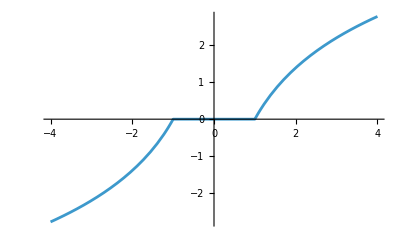

```mathematica
Plot[Im[B-B3]/.Li2Eval, {R,-4,4}]
```

```mathematica
{-(π^2+2 Li2[-R]-2 Li2[R])/π, (2 (BW[-R]-BW[R]))/π}/.Li2Eval/.BWEval/.{R->-.3+.4I}
```

{-3.50707+0.513999 ⅈ,-0.874802}

```mathematica
BWEval
```

{BW[x_]:>Im[PolyLog[2,x]]+Arg[1-x] Log[Abs[x]]}

```mathematica
{B, -(π^2+2 Li2[-R]-2 Li2[R])/π, (2 (BW[-R]-BW[R]))/π}/.Li2Eval/.BWEval/.{R->Exp[Pi I m/2]}/.{m->0}
```

Infinity::indet: Indeterminate expression ⅈ π+-∞+∞ encountered.

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{Indeterminate,-π/2,0}

```mathematica
1/U^2/.disc0sol/.{R->lam^(1/4)}//PowerExpand//Simplify
```

{1/(4 (-1+√lam)^2),1/(4 (-1+√lam)^2),1/(4 (1+√lam)^2),1/(4 (1+√lam)^2)}

```mathematica
disc0sol/.{R->1}
```

{{U→0},{U→0},{U→-4},{U→4}}